```mathematica
(*Pour mu,lam,eps = {2,5,0.1}, un seul min du pot (réel)*)
(*Pour mu,lam,eps = {2,5,0.2}*)
Needs["VariationalMethods`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
cons=Sqrt[mu^2/lam];
mu=2;lam=5;eps=0.2;
pot[x[t_]]:=(lam/8)(x[t]^2-mu^2/lam)^2+(eps/(2*cons))(x[t]-cons);
lag[x[t_]]:=t^3((1/2)(D[x[t],t])^2+pot[x[t]]);
sln=EulerEquations[lag[x[t]],x[t],t];
V[x_]:=(lam/8)(x^2-mu^2/lam)^2+(eps/(2*cons))(x-cons);
```

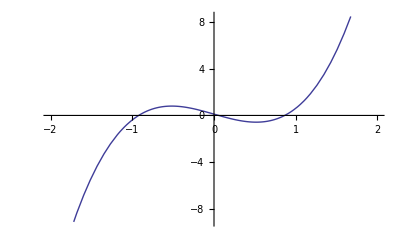

```mathematica
V'[x];
Plot[V'[x],{x,-2,2}]
```

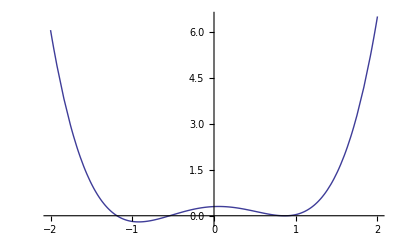

```mathematica
Plot[V[x],{x,-2,2}]
```

```mathematica
sln2=x''[t]+(3/t)(x'[t]) - (D[pot[x[t]],t]/. x'[t]->1 )
```

-0.111803-5/2 x[t] (-4/5+x[t]^2)+(3 x'[t])/t+x''[t]

```mathematica
D[V[x],x]
```

1+5/2 x (-4/5+x^2)

```mathematica
max=FindMinimum[V[x],{x,-1}]
xmax=x/.max[[2]];
max2=FindMinimum[V[x],{x,3}]
xmax2=x/.max2[[2]];
Solve[D[V[x],x]==0,x]
```

{-0.201516,{x→-0.921167}}

{-0.00161466,{x→0.865044}}

{{x→-0.921167},{x→0.0561227},{x→0.865044}}

```mathematica
xmax
xmax2
```

-0.921167

0.865044

```mathematica
0.8650443081160301
x'[t]
```

0.865044

x'[t]

```mathematica
∫x'[t]ⅆt
```

x[t]

```mathematica
tmin=2;
tmax=4;
eps=2*cons;
solution=NDSolve[{sln2==0,x[tmin]==xmax+0.1,x'[tmin]==100},x[t],{t,tmin,tmax}];
psi[t_]=x[t]/.solution[[1]];
Plot[psi[t],{t,tmin,tmax}]
```

NDSolve::ndsz: At t == 2.19305, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

```mathematica
1
```

```mathematica
∫x'[t]ⅆt
```

```mathematica
D[x[t], t]
```

```mathematica
lag[x[t]]
```

```mathematica
y=t^3 (0.05590169943749475 (-2/(√5)+x[t])+5/8 (-4/5+x[t]^2)^2+x'[t]/2);
```

```mathematica
allo=EulerEquations[y,x[t],t]
```

```mathematica
D[lag[x[t]],x'[t]]
```